# Hermite Polynomial

### Author

Eric W. Weisstein
September 14, 2008

This notebook downloaded from http://mathworld.wolfram.com/notebooks/SpecialFunctions/HermitePolynomial.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/HermitePolynomial.html.

©2008 Wolfram Research, Inc. except for portions noted otherwise

## Enumeration

```mathematica
poly=HermiteH;
```

```mathematica
poly[#,x]&/@Range[0,10]//ColumnForm//TraditionalForm
```

1
2 x
4 x^2-2
8 x^3-12 x
16 x^4-48 x^2+12
32 x^5-160 x^3+120 x
64 x^6-480 x^4+720 x^2-120
128 x^7-1344 x^5+3360 x^3-1680 x
256 x^8-3584 x^6+13440 x^4-13440 x^2+1680
512 x^9-9216 x^7+48384 x^5-80640 x^3+30240 x
1024 x^10-23040 x^8+161280 x^6-403200 x^4+302400 x^2-30240

```mathematica
DeleteCases[CoefficientList[poly[#,x],x],0]&/@Range[0,10]
```

{{1},{2},{-2,4},{-12,8},{12,-48,16},{120,-160,32},{-120,720,-480,64},{-1680,3360,-1344,128},{1680,-13440,13440,-3584,256},{30240,-80640,48384,-9216,512},{-30240,302400,-403200,161280,-23040,1024}}

```mathematica
Flatten[%]
```

{1,2,-2,4,-12,8,12,-48,16,120,-160,32,-120,720,-480,64,-1680,3360,-1344,128,1680,-13440,13440,-3584,256,30240,-80640,48384,-9216,512,-30240,302400,-403200,161280,-23040,1024}

## Plot

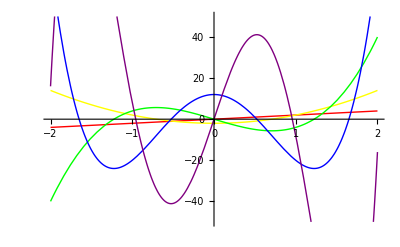

```mathematica
Plot[Evaluate[Table[HermiteH[n,x],{n,5}]],{x,-2,2},PlotStyle->{Red,Yellow,Green,Blue,Purple},PlotRange->50]
```

## Definitions

```mathematica
Expand[Table[{n,
HermiteH[n,x],
Coefficient[Series[Exp[2x t-t^2],{t,0,n}]n!,t,n],
(-1)^n Exp[x^2]D[Exp[-x^2],{x,n}],
Exp[x^2/2]Nest[(x#-D[#,x])&,Exp[-x^2/2],n]
},{n,5}]]//TableForm
```

1 | 2 x | 2 x | 2 x | 2 x
2 | -2+4 x^2 | -2+4 x^2 | -2+4 x^2 | -2+4 x^2
3 | -12 x+8 x^3 | -12 x+8 x^3 | -12 x+8 x^3 | -12 x+8 x^3
4 | 12-48 x^2+16 x^4 | 12-48 x^2+16 x^4 | 12-48 x^2+16 x^4 | 12-48 x^2+16 x^4
5 | 120 x-160 x^3+32 x^5 | 120 x-160 x^3+32 x^5 | 120 x-160 x^3+32 x^5 | 120 x-160 x^3+32 x^5

```mathematica
Table[(-1)^n Sqrt[π]/2 Exp[x^2]D[Erf[x],{x,n+1}]-HermiteH[n,x],{n,10}]//Simplify
```

{0,0,0,0,0,0,0,0,0,0}

## EGF

```mathematica
GeneratingFunction[HermiteH[n,x],n,t]
```

DifferentialRoot[Function[{𝓎,𝓍},{-1+(-1+2 x) 𝓍+(1-2 x 𝓍+2 𝓍^2) 𝓎[𝓍]+2 𝓍^3 𝓎'[𝓍]==0,𝓎[0]==1,𝓎'[0]==1}]][t]

```mathematica
TimeConstrained[FunctionExpand[%],60]//Timing
```

{53.3584,$Aborted}

```mathematica
Sum[HermiteH[n,x] t^n/(n!),{n,0,∞}]
```

ⅇ^(-t^2+2 t x)

```mathematica
SeriesCoefficient[ⅇ^(-t^2+2 t x),{t,0,n}]
```

Piecewise[{{HermiteH[n,x]/(n!), n≥0}, {0, True}}]

## Orthogonality

```mathematica
Integrate[Exp[-x^2]HermiteH[m,x]HermiteH[n,x],{x,-∞,∞}]
```

∫_(-∞)^∞ ⅇ^(-x^2) HermiteH[m,x] HermiteH[n,x]ⅆx

```mathematica
Integrate[Exp[-x^2]HermiteH[n,x]HermiteH[n,x],{x,-∞,∞}]
```

∫_(-∞)^∞ ⅇ^(-x^2) HermiteH[n,x]^2ⅆx

```mathematica
u[n_,x_]:=Sqrt[a/(Sqrt[π]n! 2^n)]HermiteH[n,a x]Exp[-a^2 x^2/2]
```

```mathematica
{PowerExpand@Table[Integrate[u[n,x]D[u[m,x],x],{x,-∞,∞},GenerateConditions->False],{m,5},{n,5}]//MatrixForm,Table[Which[
m==n+1,a Sqrt[(n+1)/2],
m==n-1,-a Sqrt[n/2],
True,0],
{m,5},{n,5}]//MatrixForm}
```

{(0 | -a | 0 | 0 | 0
a | 0 | -√(3/2) a | 0 | 0
0 | √(3/2) a | 0 | -√2 a | 0
0 | 0 | √2 a | 0 | -√(5/2) a
0 | 0 | 0 | √(5/2) a | 0),(0 | -a | 0 | 0 | 0
a | 0 | -√(3/2) a | 0 | 0
0 | √(3/2) a | 0 | -√2 a | 0
0 | 0 | √2 a | 0 | -√(5/2) a
0 | 0 | 0 | √(5/2) a | 0)}

```mathematica
{PowerExpand@Table[Integrate[u[n,x]u[m,x],{x,-∞,∞},GenerateConditions->False],{m,5},{n,5}]//MatrixForm,Table[KroneckerDelta[m,n],
{m,5},{n,5}]//MatrixForm}
```

{(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)}

## Discriminant

```mathematica
Product[k^k,{k,n}]
```

Hyperfactorial[n]

```mathematica
Table[Hyperfactorial[n],{n,6}]
```

{1,4,108,27648,86400000,4031078400000}

```mathematica
Table[2^(3n(n-1)/2)Hyperfactorial[n],{n,6}]
```

{1,32,55296,7247757312,92771293593600000,141830962344853556428800000}

## Identities

### H_n(x)==(2 x)^n _2 F_0(-n/2,-1/2 (n-1);;-1/x^2)

```mathematica
FullSimplify[(2x)^n HypergeometricPFQ[{-n/2,-(n-1)/2},{},-1/x^2],n∈Integers&&n≥0]
```

2^n x^n (x^2)^(-n/2) HypergeometricU[-n/2,1/2,x^2]

```mathematica
Subtract@@@Table[{HermiteH[n,x],(2x)^n HypergeometricPFQ[{-n/2,-(n-1)/2},{},-1/x^2]}/.{n->Random[Integer,{0,50}],x->Random[Complex,5(I+1){-1,1},100]},{20}]//Chop//Union
```

{0}

### H_n(x)==2^n x^n (x^2)^(-n/2) U(-n/2,1/2,x^2)

```mathematica
Subtract@@@Table[{HermiteH[n,x],2^n x^n (x^2)^(-n/2) HypergeometricU[-n/2,1/2,x^2]}/.{n->Random[Integer,{0,50}],x->Random[Complex,5(I+1){-1,1},100]},{20}]//Chop//Union
```

{0}

```mathematica
Subtract@@@Table[{HermiteH[n,x],2^n  HypergeometricU[-n/2,1/2,x^2]}/.{n->Random[Integer,{0,50}],x->Random[Complex,5(I+1){0,1},100]},{20}]//Chop//Union
```

{0}

### H_n(-x)==(-1)^n H_n(x)

```mathematica
FullSimplify[HermiteH[n,-x]-(-1)^n HermiteH[n,x],n∈Integers&&n≥0]
```

HermiteH[n,-x]-(-1)^n HermiteH[n,x]

```mathematica
FunctionExpand[HermiteH[n,-x],n∈Integers&&n≥0]
```

HermiteH[n,-x]

```mathematica
Table[HermiteH[n,-x]-(-1)^n HermiteH[n,x],{n,0,10}]
```

{0,0,0,0,0,0,0,0,0,0,0}

#### v5.2

```mathematica
HermiteH[n,-x]
```

HermiteH[n,-x]

#### v6

```mathematica
HermiteH[n,-x]
```

HermiteH[n,-x]

#### V7

```mathematica
HermiteH[n,-x]
```

HermiteH[n,-x]

```mathematica
FunctionExpand[HermiteH[n,-x],n∈Integers&&n≥0]
```

HermiteH[n,-x]

## Sum Identities

### ∑_(k=0)^n (n k) H_k(y) H_(n-k)(x)==2^(n/2) H_n(1/(√2) (x+y))

```mathematica
Expand[Table[Sum[Binomial[n,k]HermiteH[k,y]HermiteH[n-k,x],{k,0,n}]-2^(n/2)HermiteH[n,2^(-1/2)(x+y)],{n,0,10}]]
```

{0,0,0,0,0,0,0,0,0,0,0}

#### V7

```mathematica
Sum[Binomial[n,k]HermiteH[k,y]HermiteH[n-k,x],{k,0,n}]
```

2^(n/2) HermiteH[n,(x+y)/(√2)]

### ∑_(k=0)^n (n k) H_k(x) (2 y)^(n-k)-H_n(x+y)

#### V7

```mathematica
Sum[Binomial[n,k]HermiteH[k,x](2y)^(n-k),{k,0,n}]
```

HermiteH[n,x+y]

### ∑_(k=0)^n (-1)^(n-k) (n k) H_n(k)==2^n n!

#### V6

```mathematica
Sum[(-1)^(n-k)Binomial[n,k]HermiteH[n,k],{k,0,n}]
```

∑_(k=0)^n (-1)^(-k+n) Binomial[n,k] HermiteH[n,k]

```mathematica
Table[2^n n!,{n,0,5}]
```

{1,2,8,48,384,3840}

```mathematica
Table[Sum[(-1)^(n-k)Binomial[n,k]HermiteH[n,k],{k,0,n}],{n,0,5}]
```

{1,2,8,48,384,3840}

#### V7

```mathematica
Sum[(-1)^(n-k)Binomial[n,k]HermiteH[n,k],{k,0,n}]
```

2^n n!

### H_n(x+y)==(H+2 y)^n

```mathematica
Subtract@@@Expand[Table[{HermiteH[n,x+y],Expand[(H+2y)^n]},{n,0,10}]/.H^n_.:>HermiteH[n,x]]//Union
```

{0}

### H_n(x)==H_n(0)+∑_(m=0)^⌊n/2⌋ ∑_(k=1)^(n-2 m) (𝒮_(n-2 m)^(k) (-1)^k (-x)_k ((-1)^m 2^(n-2 m) n!))/((n-2 m)! m!)

#### V6

```mathematica
Subtract@@@Table[{HermiteH[n,x],HermiteH[n,0]+Sum[StirlingS2[n-2m,k](-1)^k Pochhammer[-x,k]((-1)^m 2^(n-2m)n!)/((n-2m)!m!),{m,0,Floor[n/2]},{k,n-2m}]},{n,10}]//Expand//Union
```

{0}

#### V7

```mathematica
HermiteH[n,0]+Sum[StirlingS2[n-2m,k](-1)^k Pochhammer[-x,k]((-1)^m 2^(n-2m)n!)/((n-2m)!m!),{m,0,Floor[n/2]},{k,n-2m}]
```

(2^n √π)/Gamma[(1-n)/2]+∑_(m=0)^Floor[n/2] ∑_k^(-2 m+n) ((-1)^(k+m) 2^(-2 m+n) n! Pochhammer[-x,k] StirlingS2[-2 m+n,k])/(m! (-2 m+n)!)

### H_(2 k)(x)==(-2)^k (2 k-1)!! _1 F_1(-k;1/2;x^2)

```mathematica
(-1)^k 2^k(2k-1)!!(1+Sum[Product[-4k+4l,{l,0,j-1}]/((2j)!)x^(2j),{j,k}])
```

(-2)^k (-1+2 k)!! Hypergeometric1F1[-k,1/2,x^2]

```mathematica
FullSimplify[(-2)^k (-1+2 k)!! Hypergeometric1F1[-k,1/2,x^2],k∈Integers&&k>0]
```

(-2)^k (-1+2 k)!! Hypergeometric1F1[-k,1/2,x^2]

```mathematica
Table[(-2)^k (-1+2 k)!! Hypergeometric1F1[-k,1/2,x^2]-HermiteH[2k,x],{k,0,5}]//Expand
```

{0,0,0,0,0,0}

```mathematica
FullSimplify[(-2)^k (-1+2 k)!! Hypergeometric1F1[-k,1/2,x^2]-HermiteH[2k,x],k∈Integers&&k>0]
```

-HermiteH[2 k,x]+(-2)^k (-1+2 k)!! Hypergeometric1F1[-k,1/2,x^2]

```mathematica
FunctionExpand[(-2)^k (-1+2 k)!! Hypergeometric1F1[-k,1/2,x^2],k∈Integers&&k>0]
```

(-1)^k 2^(-1/4+1/4 (-1)^(2 k)+2 k) π^(-1/4-1/4 (-1)^(2 k)) Gamma[1/2+k] Hypergeometric1F1[-k,1/2,x^2]

### H_(2 k+1)(x)==(-1)^k 2^(k+1) x (2 k+1)!! _1 F_1(-k;3/2;x^2)

```mathematica
(-1)^k 2^(k+1)(2k+1)!!(x+Sum[Product[-4k+4l,{l,0,j-1}]/((2j+1)!)x^(2j+1),{j,k}])
```

(-1)^k 2^(1+k) (1+2 k)!! (x+x (-1+Hypergeometric1F1[-k,3/2,x^2]))

```mathematica
FullSimplify[(-1)^k 2^(1+k) (1+2 k)!! (x+x (-1+Hypergeometric1F1[-k,3/2,x^2])),k∈Integers&&k>0]
```

(-1)^k 2^(1+k) x (1+2 k)!! Hypergeometric1F1[-k,3/2,x^2]

```mathematica
Table[(-1)^k 2^(1+k) x (1+2 k)!! Hypergeometric1F1[-k,3/2,x^2]-HermiteH[2k+1,x],{k,0,5}]//Expand
```

{0,0,0,0,0,0}

```mathematica
FullSimplify[(-1)^k 2^(1+k) x (1+2 k)!! Hypergeometric1F1[-k,3/2,x^2]-HermiteH[2k+1,x],k∈Integers&&k>0]
```

-HermiteH[1+2 k,x]+(-1)^k 2^(1+k) x (1+2 k)!! Hypergeometric1F1[-k,3/2,x^2]

```mathematica
FunctionExpand[(-2)^k (-1+2 k)!! Hypergeometric1F1[-k,1/2,x^2],k∈Integers&&k>0]
```

(-1)^k 2^(-1/4+1/4 (-1)^(2 k)+2 k) π^(-1/4-1/4 (-1)^(2 k)) Gamma[1/2+k] Hypergeometric1F1[-k,1/2,x^2]

## Recurrence Relation

```mathematica
RSolve[{H[n+1,x]==2x H[n,x]-2n H[n-1,x],H[0,x]==1,H[1,x]==2x},H[n,x],n]
```

{{H[n,x]→HermiteH[n,x]}}

```mathematica
D[HermiteH[n,x],x]
```

2 n HermiteH[-1+n,x]

## Generalized

### EGF==exp(m t x-t^m)

```mathematica
SeriesCoefficient[Exp[m x t-t^m],{t,0,n}]
```

SeriesCoefficient[ⅇ^(-t^m+m t x),{t,0,n}]

```mathematica
Series[Exp[m x t-t^m],{t,0,2}]
```

ⅇ^(-t^m+(m x t+O[t]^3))

```mathematica
Series[Exp[m x t-t],{t,0,2}]
```

1+(-1+m x) t+1/2 (1-2 m x+m^2 x^2) t^2+O[t]^3

### He_n(x)

```mathematica
Expand[Table[{n,2^(-n/2)HermiteH[n,x/Sqrt[2]]},{n,5}]]//TableForm//TraditionalForm
```

1 | x
2 | x^2-1
3 | x^3-3 x
4 | x^4-6 x^2+3
5 | x^5-10 x^3+15 x

```mathematica
DeleteCases[CoefficientList[2^(-#/2)HermiteH[#,x/Sqrt[2]],x],0]&/@Range[0,10]
```

{{1},{1},{-1,1},{-3,1},{3,-6,1},{15,-10,1},{-15,45,-15,1},{-105,105,-21,1},{105,-420,210,-28,1},{945,-1260,378,-36,1},{-945,4725,-3150,630,-45,1}}

```mathematica
Flatten[%]
```

{1,1,-1,1,-3,1,3,-6,1,15,-10,1,-15,45,-15,1,-105,105,-21,1,105,-420,210,-28,1,945,-1260,378,-36,1,-945,4725,-3150,630,-45,1}